```mathematica
f[x_]:=Sin[x ^ 2] + 1.5;
start = 0;
end = 2 * Pi;
(*numberOfParts = 10;*)
```

# Riemann Sum

Approximating the definite integral

## Introduction

Let’s suppose you want to obtain the area under the curve in a plot

Example curve and area

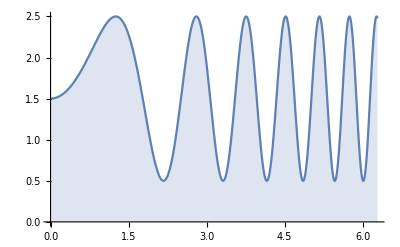

```mathematica
functionPlot :=Plot[f[x], {x, start, end}, Filling->Axis, PlotRange->{{start, end},{0, 2.5}}]; functionPlot
```

If you were drawing the curve in paper, it is not really possible to measure it directly as it is. The most naive approach is to draw geometrical figures to which is know how to calculate their area. For example, rectangles.

Representing the curve as rectangles

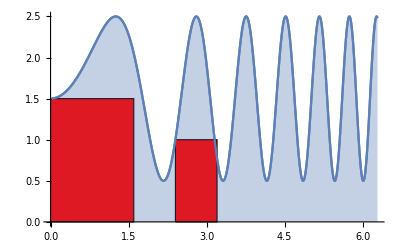

```mathematica
rectCoord = {
{{0,0},{1.6,0},{1.6, 1.5},{0,1.5}},
{{2.4, 0},{3.2,0},{3.2,1},{2.4,1}}
};
bars =Map[ Graphics[{
		EdgeForm[{Thick, Black}],
		Red,
		Polygon[#]
}]&,
rectCoord
];
Show @ Flatten[{functionPlot, bars, functionPlot}]
```

We can simplify our approximation making rectangle’s height be dependant of the curve’s values, for example

Now the rectangle height depends on the curve height

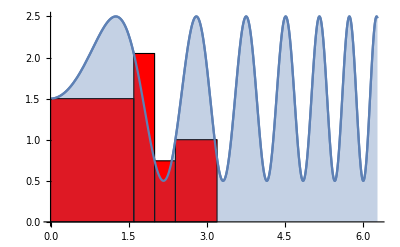

```mathematica
rectXCoord = {
{0,1.6},
{2.4,3.2},
{1.6,2},
{2,2.4}
};
bars =Map[ Graphics[{
EdgeForm[{Thick, Black}],
Red,
Module[{height},
height = f[#[[1]]];
Polygon[{{#[[1]],0},{#[[2]],0},{#[[2]], height},{#[[1]],height}}]
]
}]&,
rectXCoord
];
Show @ Flatten[{functionPlot, bars, functionPlot}]
```

In this example, the height is equal to the value of the function in the x value of the left-most side of the rectangle. The total area of the rectangles with this approach is:
∑_(x∈X) =f(x_Left) * (x_Right - x_Left)
where the elements in X contain

Direction

```mathematica
Code
```

Code

## Add more sections as needed to explain the topic (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)